The chi - square  statistic follows the following distribution (see Wikipedia) :

```mathematica
chisquare[k_,x_]=1/(2^(k/2)*Gamma[k/2])x^(k/2-1)*Exp[-x/2]
```

(2^(-k/2) ⅇ^(-x/2) x^(-1+k/2))/Gamma[k/2]

k is the number of degrees of freedom, which in our case is the number of fitted parameters. We are fitting one parameter, < σv >, for each value of mass, so in our case k=1.

Say we discover dark matter.  Wilks' theorem tells us that 2 Δ ln L (which is a function of  < σv >) follows the chi - square distribution, so if I want to find what value of 2 Δ ln L corresponds to 95% exclusion, I can integrate the chi-square distribution and find where that integral = 0.95.00

```mathematica
FindRoot[Integrate[chisquare[1,x],{x,0,x0}]==.95,{x0,.5}]
```

{x0→3.84146}

So values of < σv > that give 2 Δ ln L > 3.84 are excluded at 95 % CL. These will be values of < σv > that are either too big or too small relative to the actual value.

However, we have not discovered dark matter. Instead we are just setting an upper limit on the cross section. So to find the values that are excluded at 95 % CL, we have to find where the previous integral is actually equal to 0.90

```mathematica
FindRoot[Integrate[chisquare[1,x],{x,0,x0}]==.90,{x0,.5}]
```

{x0→2.70554}

Which is the number you are familiar with. The idea here is that we can only exclude values of < σv > that are too large, not too small as before, so the “missing” 5% comes from the fact that the low values are now allowed.

I' m hiding alot in this discussion -- mainly how this is all ultimately derived from Gaussian statistics, making the whole one - sided limit argument a bit more sensible, but that is talked about a bit in the review I sent you, I think...

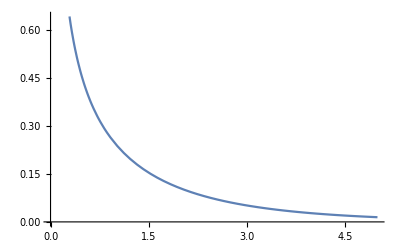

```mathematica
Plot[{chisquare[1,x]},{x,0,5},PlotLegends->"Expressions"]
```

```mathematica
Integrate[chisquare[1,x],{x,0,2.705}]
```

0.899966